```mathematica
<< MaTeX`
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{1,1}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

## Optimisation of MFPT (Figure 4)

```mathematica
T[r1_,r2_]:=(1-Exp[- Sqrt[r1]])/(r1 Exp[- Sqrt[r1]])+(1-Exp[- Sqrt[r1]])/(r2 Exp[-Sqrt[r1]])
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
r2et1=Import["Simulations/Intel_MFTP_MappingR1_r2=1_0_runs=100000.dat"];
```

```mathematica
r2et5=Import["Simulations/Intel_MFTP_MappingR1_r2=5_0_runs=100000.dat"];
```

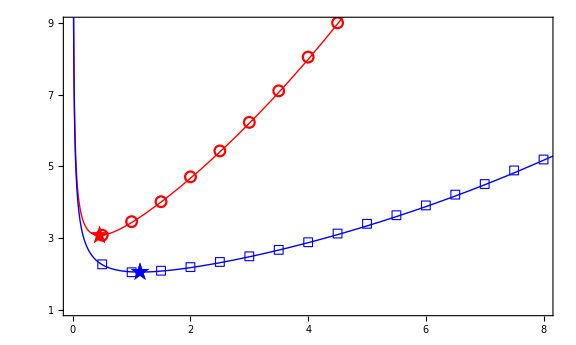

```mathematica
xm=0;xM=8;ym=1;yM=9;ΔxM=2;Δxm=1;ΔyM=2;Δym=1;
Tr1r2=Show[ 
ListPlot[{r2et1,r2et5},PlotRange->{{xm,xM},{ym,yM}},PlotMarkers->{Graphics[{Red,Circle[]},ImageSize->11,ImagePadding->2],Graphics[{EdgeForm[Blue],FaceForm[],Rectangle[]},ImageSize-> 9]},LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],Frame->True,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["r_1",Magnification->2],MaTeX["T(r_1,r_2)",Magnification->2]},ImageSize->Large,AspectRatio->0.6,PlotLegends->Placed[{{MaTeX["r_2=1",Magnification->1.5],MaTeX["r_2=5",Magnification->1.5]}},{Left,Top}],
FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}}],Plot[{T[r1,1],T[r1,5]},{r1,0.01,15},PlotStyle->{{Red,Thick},{Blue,Thick}}],
ListPlot[{{r1/.Last[FindMinimum[T[r1,1],{r1,0.5}]],FindMinimum[T[r1,1],{r1,0.5}][[1]]}},PlotMarkers->Style["★",Red,20]],ListPlot[{{r1/.Last[FindMinimum[T[r1,5],{r1,0.5}]],FindMinimum[T[r1,5],{r1,0.5}][[1]]}},PlotMarkers->Style["★",Blue,20]]]
```

### Analytical approximation (obtaining Eq. (54))

```mathematica
r1OptAn1[a_]:=a- a^(3/2)+(5 a^2)/6;
```

### Inset plot Figure 4

```mathematica
LTicksLog2=Flatten[{Table[{10^i,Superscript[10,i],{0.04,0},Thickness[0.004]},{i,-3,3,1}],Flatten[Table[{j *10^i,"",{0.02,0},Thickness[0.002]},{i,-3,3,1},{j,1,9,1}],1]},1];
```

```mathematica
STicksLog2=Flatten[{Table[{10^i,"",{0.04,0},Thickness[0.004]},{i,-3,3,1}],Flatten[Table[{j *10^i,"",{0.02,0},Thickness[0.002]},{i,-3,3,1},{j,1,9,1}],1]},1];
```

```mathematica
f[r2_]:=r1/.FindRoot[2 r2+ⅇ^(√r1) (-2 r2+√r1 (r1+r2) )==0,{r1,Min[r2,2.4]}]
```

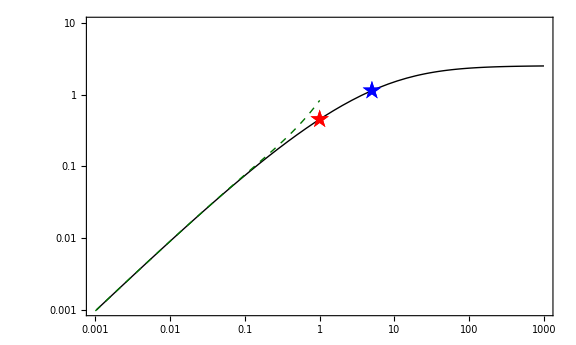

```mathematica
r1vsr2P1=Show[LogLogPlot[{f[r2]},{r2,0.001,1000},PlotRange-> {{0.001,1000},{0.001,10}},PlotStyle->{{Black,Thick}},LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],Frame->True,FrameStyle->Directive[Black,25,FontFamily->"Times New Roman",Thickness[0.004]],Exclusions-> None,FrameTicks->{{LTicksLog2,STicksLog2},{LTicksLog2,STicksLog2}}  
,FrameLabel->{MaTeX["r_2",Magnification->3],MaTeX["r_1^{\\scriptsize\\mbox{Opt}}",Magnification->3]} 
,ImageSize->Large,AspectRatio->0.6],LogLogPlot[{r1OptAn1[r2]},{r2,0.001,1},PlotStyle->{Darker[Darker[Green]],Thick,Dashed}],ListLogLogPlot[{{1,r1/.Last[FindMinimum[T[r1,1],{r1,0.5}]]}},PlotMarkers->Style["★",Red,20]],ListLogLogPlot[{{5,r1/.Last[FindMinimum[T[r1,5],{r1,0.5}]]}},PlotMarkers->Style["★",Blue,20]]](*,Background-> RGBColor[{252,242,234,255}/255]*)
```